## Markov Chains Test

The transition matrix is (1/3 | 1/3 | 1/3
1/2 | 0 | 1/2
1/2 | 1/2 | 0) and the initial state is (1
0
0).
The eigensystem is (1
-1/2
-1/6)  and (1 | 1 | 1
0 | -1 | 1
-4/3 | 1 | 1).

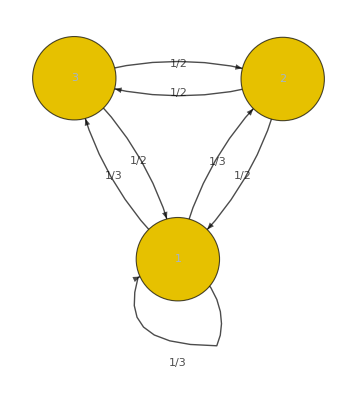

```mathematica
pMatrix = {{1/3,1/3,1/3},{1/2,0,1/2},{1/2,1/2,0}};
s0={1,0,0};
{eVal,eVec}=Eigensystem[pMatrix];

StringForm["The transition matrix is `` and the initial state is ``.
The eigensystem is ``  and ``.",pMatrix//MatrixForm,s0//MatrixForm,eVal//MatrixForm,eVec//MatrixForm]

mp =DiscreteMarkovProcess[s0,pMatrix];
mg=Graph[mp, EdgeLabels->{DirectedEdge[i_,j_]:>pMatrix[[i,j]]},EdgeStyle->Directive[Black],VertexSize->0.4]
```

## Test of the Invariant Distribution

```mathematica
pMatrix2={{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}};
pMatrix2//MatrixForm
Eigenvectors[Transpose[pMatrix2]]
```

(0 | 1/2 | 1/2
1/2 | 0 | 1/2
1/2 | 1/2 | 0)

{{1,1,1},{-1,0,1},{-1,1,0}}